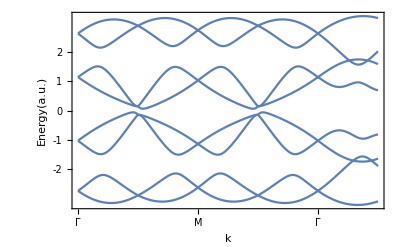

```mathematica
k1f[s_]:=(s-π)HeavisideTheta[π-s]+(s-2π)*HeavisideTheta[2π-s]+(3π-s)*HeavisideTheta[3π-s]+1/(√2)(4π-s)*HeavisideTheta[4π-s]+1/(√2)(s-4π)HeavisideTheta[(4+√2)π-s];
k2f[s_]:=(π-s)HeavisideTheta[π-s]+(s-2π)HeavisideTheta[2π-s]+(s-3π)HeavisideTheta[3π-s]+((4+2 √2)π-(1+1/(√2))s)HeavisideTheta[4π-s]+1/(√2)(s-4π)HeavisideTheta[(4+√2)π-s];
H[t1_,t2_,t4_,k1_,k2_]:={{0, t1,t2*ⅇ^(-ⅈ*k1),t1,0,-t4*((√2)/2+(√2)/2 ⅈ),t4*ⅇ^(-ⅈ*k1),t4*(-(√2)/2+(√2)/2 ⅈ)},{t1,0,t1,t2 ⅇ^(-ⅈ*k2),t4*((√2)/2+(√2)/2 ⅈ),0,t4*(-(√2)/2+(√2)/2 ⅈ),t4*(-ⅈ*ⅇ^(-ⅈ*k2))},{t2 ⅇ^(ⅈ*k1),t1,0,t1,-t4*ⅇ^(ⅈ*k1),t4*((√2)/2-(√2)/2 ⅈ),0,t4*((√2)/2+(√2)/2 ⅈ)},{t1,t2 ⅇ^(ⅈ k2),t1,0,t4*((√2)/2-(√2)/2 ⅈ),t4*(ⅈ*ⅇ^(ⅈ*k2)),t4*(-(√2)/2-(√2)/2 ⅈ),0},{0,-t4*(-(√2)/2+(√2)/2 ⅈ),-t4*ⅇ^(-ⅈ*k1),t4*((√2)/2+(√2)/2 ⅈ),0,t1,t2*ⅇ^(-ⅈ*k1),t1},{t4*(-(√2)/2+(√2)/2 ⅈ),0,t4*((√2)/2+(√2)/2 ⅈ),t4*(-ⅈ*ⅇ^(-ⅈ*k2)),t1,0,t1,t2*ⅇ^(-ⅈ*k2)},{t4*ⅇ^(ⅈ*k1),t4*(-(√2)/2-(√2)/2 ⅈ),0,t4*(-(√2)/2+(√2)/2 ⅈ),t2*ⅇ^(ⅈ*k1),t1,0,t1},{t4*(-(√2)/2-(√2)/2 ⅈ),t4*(ⅈ*ⅇ^(ⅈ*k2)),t4*((√2)/2-(√2)/2 ⅈ),0,t1,t2*ⅇ^(ⅈ*k2),t1,0}};
With[{t1=0.8,t2=1.0,t4=0.8},Plot[Sort[Re[Eigenvalues[N[H[t1,t2,t4,k1f[s*π],k2f[s*π]]]]]],{s,0,5},Frame->True,FrameTicks->{{{-2,-1,0,1,2},None},{{0,Γ},{1,Χ},{2,Μ},{3,Σ},{4,Γ},{5,M}}},FrameLabel->{"k","Energy(a.u.)"}]]
```